Plot[{Sqrt[x]},{x,0,1}]

```mathematica
Needs["PacletManager`"]
PacletInstall["C:/MaTeX-1.7.5.paclet"]
```

Paclet[MaTeX,1.7.5,<>]

```mathematica
<<MaTeX`
```

```mathematica
<<MaTeX`
MaTeX@HoldForm[Sum[1/k^2,{k,1,∞}]]
```

-Graphics-

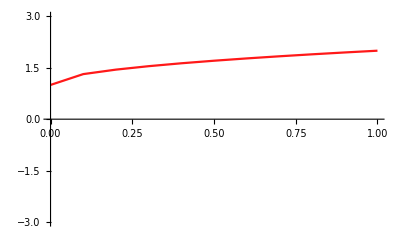

```mathematica
ListLinePlot[Table[{x,1+√x},{x,0,1,0.1}],
AxesStyle -> Black, 
PlotStyle-> Opacity[0.9, Red], 
PlotRange->{{0,1},{-3,3}}]
```

```mathematica
g[t_]:= If[t ==0,1/2,1/2-t Log[1/4(1 + √(1 + 8 Exp[-1/t]))]]
```

```mathematica
g[t_]:=1+t
```

```mathematica
FindMaximum[Evaluate[D[1/2-t Log[1/4(1 + √(1 + 8 Exp[-1/t]))],{t,1}]],t][[1]]
```

0.693147

```mathematica
f[h_,n_]:=Show[

ListLinePlot[Table[{t,g[t]},{t,0,1,0.001}],
AxesStyle -> Black, 
PlotStyle-> Opacity[0.9, Red], 
PlotRange->{{0,1},{-3,3}}, 
GridLines -> {Table[k,{k,0,1,1/n}],Table[k,{k,-3,3,h}]}],

ListLinePlot[Table[{t,g[t]},{t,0,1,1/n}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Blue],Dashed}, 
PlotRange->{{0,1},{-3,3}}],

ListLinePlot[Table[{t,g[1]+FindMaximum[Evaluate[D[g[t],{t,1}]],t][[1]]-FindMaximum[Evaluate[D[g[t],{t,1}]],t][[1]] t},{t,0,1,1/n}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Green],Dashed}, 
PlotRange->{{0,1},{-3,3}}],

ListLinePlot[RandomFunction[WienerProcess[],{0,1,0.001},50],
AxesStyle -> Black, 
PlotStyle->{{ Opacity[0.3, Black], Thickness[0.001]}}, 
PlotRange->{{0,1},{-3,3}}],

ContourPlot[Log[1+PDF[NormalDistribution[0,√t],x]],{t,0,1},{x,-3,3},ColorFunction->({Opacity[#],ColorData["SolarColors"][#]}&)]

]
```

Error bound for E_n

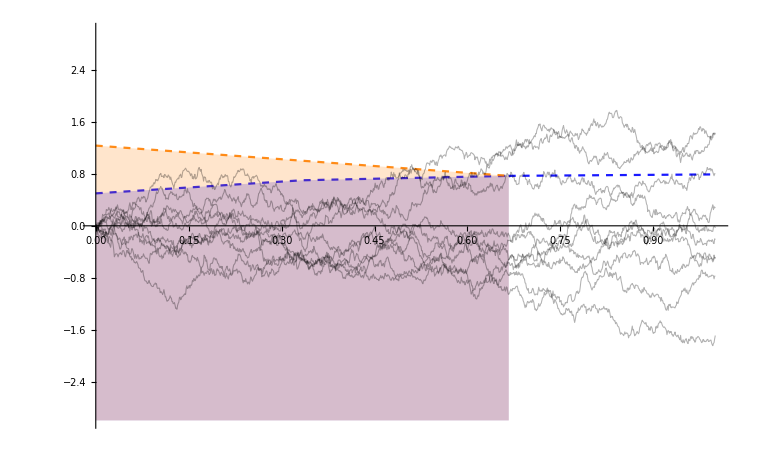

```mathematica
Show[

ListLinePlot[Table[{t,g[t]},{t,0,2/3,1/3}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Blue],Dashed}, 
PlotRange->{{0,1},{-3,3}}, 
GridLines -> {Table[k,{k,0,1,1/3}],Table[k,{k,-3,3,1/3}]},
Filling->Bottom],

ListLinePlot[Table[{t,g[t]},{t,2/3,1,1/3}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Blue],Dashed}, 
PlotRange->{{0,1},{-3,3}}, 
GridLines -> {Table[k,{k,0,1,1/3}],Table[k,{k,-3,3,1/3}]}],


ListLinePlot[Table[{t,g[2/3]+0.7 2/3 - 0.7 t},{t,0,2/3,1/3}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Orange],Dashed}, 
PlotRange->{{0,1},{-3,3}},
Filling->Bottom],

ListLinePlot[RandomFunction[WienerProcess[],{0,1,0.001},10],AxesStyle -> Black, PlotStyle->{{ Opacity[0.3, Black], Thickness[0.001]}}]

]
```

Error bound for E_k

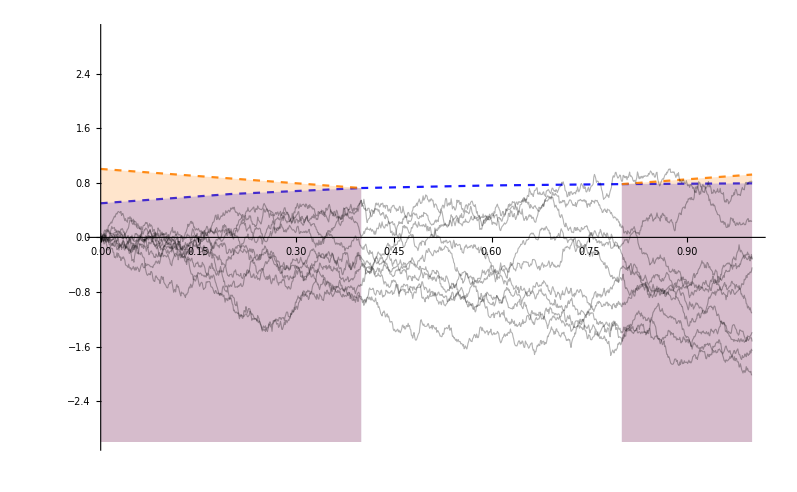

```mathematica
Show[

ListLinePlot[Table[{t,g[t]},{t,0,2/5,1/5}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9, Blue],Dashed}, 
PlotRange->{{0,1},{-3,3}}, 
GridLines -> {Table[k,{k,0,1,1/5}],Table[k,{k,-3,3,1/5}]},
Filling->Bottom],

ListLinePlot[Table[{t,g[t]},{t,2/5,4/5,1/5}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Blue],Dashed}, 
PlotRange->{{0,1},{-3,3}}],

ListLinePlot[Table[{t,g[2/5]+0.7 2/5 - 0.7 t},{t,0,2/5,1/5}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Orange],Dashed}, 
PlotRange->{{0,1},{-3,3}},
Filling->Bottom],

ListLinePlot[Table[{t,g[t]},{t,4/5,1,1/5}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9, Blue], Dashed}, 
PlotRange->{{0,1},{-3,3}}, 
GridLines -> {Table[k,{k,0,1,1/5}],Table[k,{k,-3,3,1/5}]},
Filling->Bottom],

ListLinePlot[Table[{t,g[4/5]-0.7 4/5 + 0.7 t},{t,4/5,1,1/5}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Orange],Dashed}, 
PlotRange->{{0,1},{-3,3}},
Filling->Bottom],

ListLinePlot[RandomFunction[WienerProcess[],{0,1,0.001},10],AxesStyle -> Black, PlotStyle->{{ Opacity[0.3, Black], Thickness[0.001]}}]

]
```

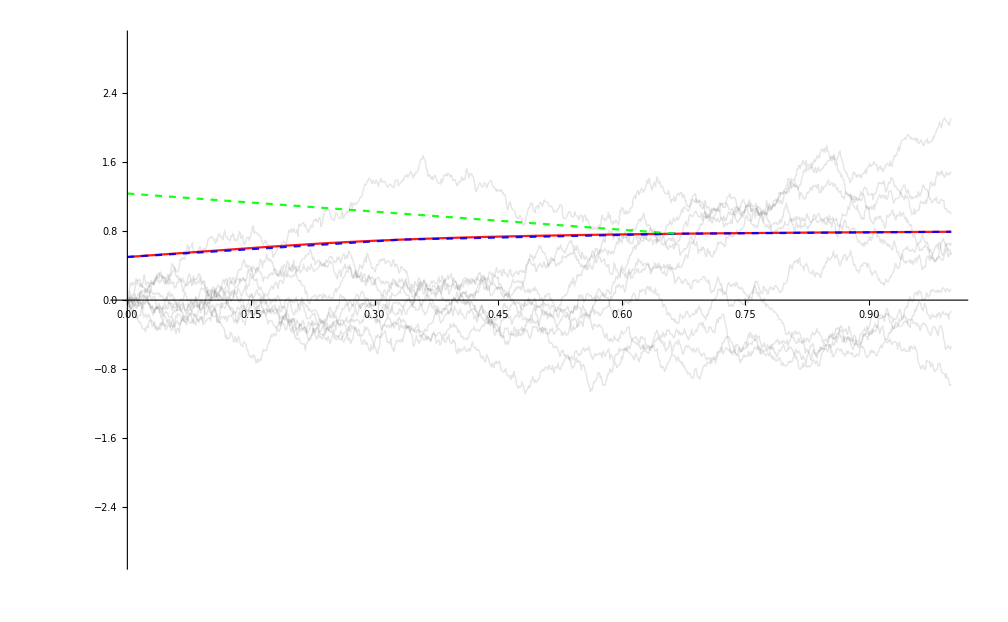

```mathematica
Show[

ListLinePlot[Table[{t,g[t]},{t,0,1,0.001}],
AxesStyle -> Black, 
PlotStyle-> Opacity[0.9, Red], 
PlotRange->{{0,1},{-3,3}}, 
GridLines -> {Table[k,{k,0,1,1/3}],Table[k,{k,-3,3,√(1/3)}]}],

ListLinePlot[Table[{t,g[t]},{t,0,1,1/3}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Blue],Dashed}, 
PlotRange->{{0,1},{-3,3}}],

ListLinePlot[Table[{t,g[2/3]+0.7 2/3 - 0.7 t},{t,0,2/3,1/3}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Green],Dashed}, 
PlotRange->{{0,1},{-3,3}}],

ListLinePlot[RandomFunction[WienerProcess[],{0,1,0.001},10],AxesStyle -> Black, PlotStyle->{{ Opacity[0.1, Black], Thickness[0.001]}}]

]
```

https://stackoverflow.com/questions/6568892/opacity-control-for-overlaying-plots

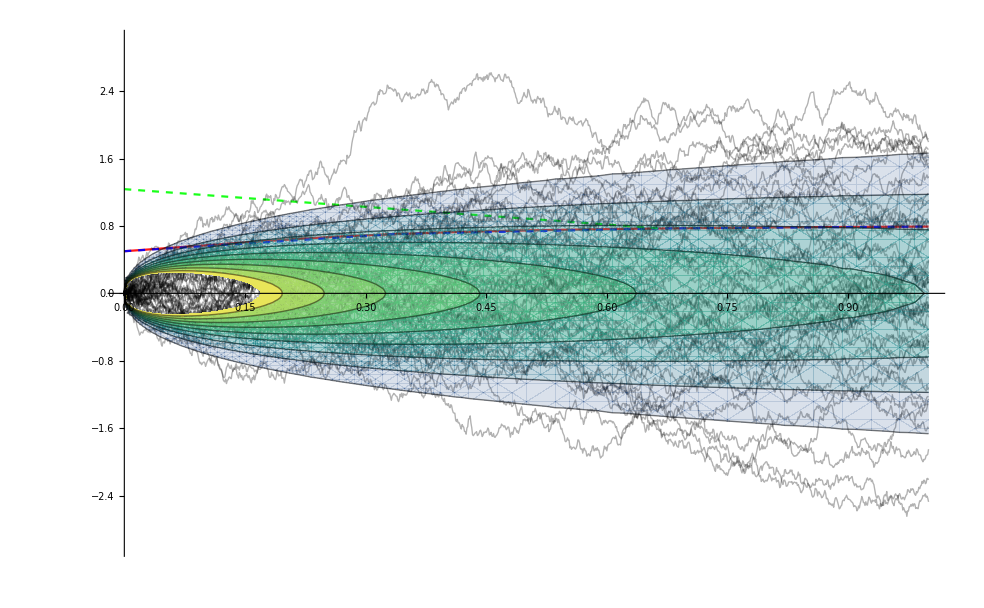

```mathematica
Show[

ListLinePlot[Table[{t,g[t]},{t,0,1,0.001}],
AxesStyle -> Black, 
PlotStyle-> Opacity[0.9, Red], 
PlotRange->{{0,1},{-3,3}}, 
GridLines -> {Table[k,{k,0,1,1/3}],Table[k,{k,-3,3,1/3}]}],


ListLinePlot[Table[{t,g[t]},{t,0,1,1/3}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Blue],Dashed}, 
PlotRange->{{0,1},{-3,3}}],

ListLinePlot[Table[{t,g[2/3]+0.7 2/3 - 0.7 t},{t,0,2/3,1/3}],
AxesStyle -> Black, 
PlotStyle-> {Opacity[0.9,Green],Dashed}, 
PlotRange->{{0,1},{-3,3}}],

ListLinePlot[RandomFunction[WienerProcess[],{0,1,0.001},50],AxesStyle -> Black, PlotStyle->{{ Opacity[0.3, Black], Thickness[0.001]}}],

ContourPlot[PDF[NormalDistribution[0,√t],x],{t,0,1},{x,-3,3},ColorFunction->({Opacity[#],ColorData["BlueGreenYellow"][#]}&)]

]
```